# NG4P05.Normally distributed random value

Выполнила  студентка 2 курса  5 группы
Кадакова Надежда
27.04.2017

## Ex.1

Предположим, что значение некоторого показателя x распределено по нормальному закону со средним μ и стандартным отклонением σ. Запишите формулу плотности распределения вероятности значений показателя x (см. [1]). Самостоятельно вычислите “Правило шести сигм” — вероятности попадания значений параметра x в промежутки (n-1)σ⩽|x-μ|⩽n σ для n=1,…,6. Самостоятельно постройте картинку, иллюстрирующую правило трёх сигм (см. Рис.1).

Напишем  функцию MyPDF-формула плотности распределения вероятности значений показателя x :

```mathematica
MyPDF[x_,μ_,σ_]:=1/(√(2 π) σ)  ⅇ^(-(x-μ)^2/(2 σ^2))
```

Для составления  таблицы  вероятности попадания значения параметра  x напишем функцию IPDF,  которая с помощью интеграла  вычисляет  площадь  под  графиком.

```mathematica
IPDF[n_]:=Round[Integrate[MyPDF[x,μ,σ],{x,μ+n*σ,μ+(n+1)*σ}],0.001]//N
```

Вероятность попадания значения параметра в промежутки (n - 1) σ ⩽ |x - μ| ⩽ nσ для n = 1, …, 6 :

```mathematica
Grid[{{"-6σ","-5σ","-4σ","-3σ","-2σ","-σ","σ","2σ","3σ","4σ","5σ","6σ"},Table[IPDF[i],{i,-6,5}]"%"},Frame->All]
```

-6σ | -5σ | -4σ | -3σ | -2σ | -σ | σ | 2σ | 3σ | 4σ | 5σ | 6σ
0. | 0. | 0.001 % | 0.021 % | 0.136 % | 0.341 % | 0.341 % | 0.136 % | 0.021 % | 0.001 % | 0. | 0.

Построим  картинку, иллюстрирующую “Правило  трех  сигм”

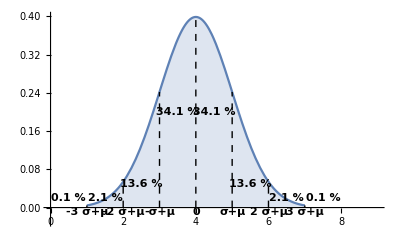

```mathematica
Module[{μ=4,σ=1},
Show[Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-3σ,μ+3σ},Filling->Axis,PlotRange->{{0,9},{-0.03,0.4}}],
Graphics[{
Table[Text[Style[i"σ+μ",Bold],{μ+i*σ,-0.01}],{i,-3,3}],Dashed,
Table[Line[{{μ+i*σ,0},{μ+i*σ,MyPDF[μ+i*σ,μ,σ]}}],{i,-3,3}],
Text[Style[IPDF[-4]*100"%",Bold],{0.5,0.02}],
Text[Style[IPDF[-3]*100"%",Bold],{1.5,0.02}],
Text[Style[IPDF[-2]*100"%",Bold],{2.5,0.05}],
Text[Style[IPDF[-1]*100"%",Bold],{3.5,0.2}],
Text[Style[IPDF[0]*100"%",Bold],{4.5,0.2}],
Text[Style[IPDF[1]*100"%",Bold],{5.5,0.05}],
Text[Style[IPDF[2]*100"%",Bold],{6.5,0.02}],
Text[Style[IPDF[3]*100"%",Bold],{7.5,0.02}]
}]
]]
```

Выпишите явно формулы для вычисления среднего значения μ и стандартного  отклонения σ по заданной выборке X. Объясните, чем стандартное отклонение отличается от среднеквадратичного отклонения.

Среднее значения μ по заданной выборке x : μ=1/n ∑_(i=1)^n x_i

Стандартное  отклонение σ по заданной выборке x : σ=√(1/(n-1) ∑_(i=1)^n (x_i-μ)^2)

Среднеквадратичное отклонение σ по заданной выборке x : σ=√(1/n ∑_(i=1)^n (x_i-μ)^2)

Среднеквадратичное отклонение - показатель рассеивания значений случайной величины относительно её математического ожидания.Стандартное отклонение - степень отклонения данных наблюдений от среднего значения.

Напишите функцию Sigma3[X], которая строит панель (см. Рис.2), иллюстрирующую соответствие заданной выборки X (под выборкой здесь понимается массив значений параметра x) правилу трёх сигм (обратите внимание на оператор BinCounts).

```mathematica
Grid[{{"-6σ","-5σ","-4σ","-3σ","-2σ","-σ","σ","2σ","3σ","4σ","5σ","6σ"},Table[IPDF[i],{i,-6,5}]"%"},Frame->All]
```

-6σ | -5σ | -4σ | -3σ | -2σ | -σ | σ | 2σ | 3σ | 4σ | 5σ | 6σ
0. | 0. | 0.001 % | 0.021 % | 0.136 % | 0.341 % | 0.341 % | 0.136 % | 0.021 % | 0.001 % | 0. | 0.

## Ex.2

Загрузите тестовые растры Test с рукописным начертанием цифр из базы данных MNIST (см. [2])

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,{TrainLabel,TrainImage}=LoadMNIST["train"]];
```

```mathematica
Map[Dimensions,{TestLabel,TestImage}=LoadMNIST["t10k"]];
```

```mathematica
DynamicModule[{m=7},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[TrainLabel⟦n⟧,Bold,24+2m]->Image[256-TrainImage⟦n⟧,"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@TrainLabel,1,Appearance->"Labeled"},Paneled->False],
Manipulate[Style[TestLabel⟦n⟧,Bold,24+2m]->Image[256-TestImage⟦n⟧,"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@TestLabel,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]]
```

В рамках данной работы в качестве объекта «Свой» используйте цифру, указанную в Вашем варианте задания. Зафиксируйте пиксель растра, находящийся в строке row и столбце col, указанные в Вашем варианте задания. Рассмотрим значение выбранного пикселя как параметр x, характеризующий цифру. Для тестовой выборки рассчитайте среднее значение и стандартное отклонение значений данного параметра. На одном графике (см. Рис.3) постройте гистограмму данной выборки и график плотности распределения нормально распределенной случайной величины с такими же средним и стандартным отклонением. На графике вертикальными штриховыми линиями отметьте границы зон ±nσ. Проверьте, соответствуют ли выбранный параметр правилу трёх сигм.

>>Выберем номер строки, столбца и цифру, исходя  из  варианта задания в xlsx-файле

```mathematica
digit=2;row=17;column=8;
data=TestImage⟦;;,row,column⟧;
```

>>Для тренировочной выборки рассчитайте среднее значение и стандартное отклонение значений данного параметра

```mathematica
σ1=StandardDeviation[data]//N;
μ1=Mean[data]//N;
```

>>На одном графике (см.Рис .3) постройте гистограмму данной выборки и график плотности распределения нормально распределенной случайной величины с такими же средним и стандартным отклонением.На графике вертикальными штриховыми линиями отметьте границы зон ±nσ.

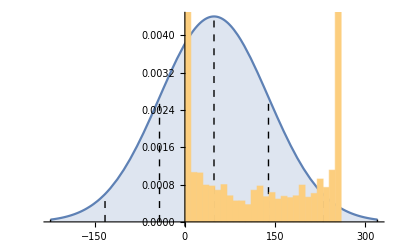

```mathematica
Module[{μ=μ1,σ=σ1},
Show[Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-3σ,μ+3σ},Filling->Axis,PlotRange->Automatic],
Graphics[{Dashed,
Table[Line[{{μ+i*σ,0},{μ+i*σ,MyPDF[μ+i*σ,μ,σ]}}],{i,-3,3}]
}],Histogram[data,Automatic,"PDF"]
]]
```

>>Проверьте, соответствуют ли выбранный параметр правилу трёх сигм.

Исходя  из полученного  графика  можно  сделать  вывод,  что данный параметр не  соответствует  правилу  “трех  сигм”, так как его  гистограмма не  соответствует графику плотности распределения нормально распределенной случайной величины

## Ex.3

Повторите исследования из п.2 для следующий вариантов параметров (см. Рис.4):

3.1. Скан-строка — сумма всех пикселей, попадающих в зафиксированную Вами (row) строку растра.

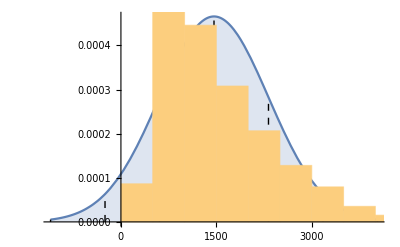

```mathematica
rowData=Plus@@#&/@TestImage⟦;;,row,;;⟧;
σr=StandardDeviation[rowData]//N;
μr=Mean[rowData]//N;
Module[{μ=μr,σ=σr},
Show[Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-3σ,μ+3σ},Filling->Axis,PlotRange->Automatic],
Graphics[{Dashed,
Table[Line[{{μ+i*σ,0},{μ+i*σ,MyPDF[μ+i*σ,μ,σ]}}],{i,-3,3}]
}],Histogram[rowData,Automatic,"PDF"]
]]
```

3.2. Скан-столбец — сумма всех пикселей, попадающих в зафиксированный Вами (col)  столбец растра.

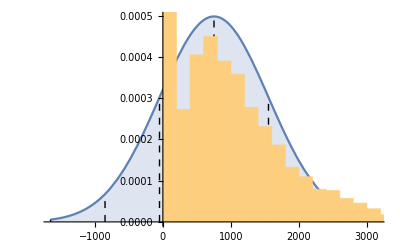

```mathematica
colData=Plus@@#&/@TestImage⟦;;,;;,column⟧;
σc=StandardDeviation[colData]//N;
μc=Mean[colData]//N;
Module[{μ=μc,σ=σc},
Show[Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-3σ,μ+3σ},Filling->Axis,PlotRange->Automatic],
Graphics[{Dashed,
Table[Line[{{μ+i*σ,0},{μ+i*σ,MyPDF[μ+i*σ,μ,σ]}}],{i,-3,3}]
}],Histogram[colData,Automatic,"PDF"]
]]
```

3.3.Скан-крест — сумма всех пикселей, попадающих в выбранные строку и столбец растра.

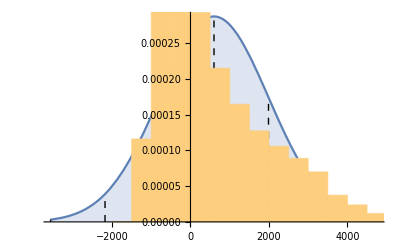

```mathematica
crossData=rowData+colData-rowData⟦column⟧;
σcr=StandardDeviation[crossData]//N;
μcr=Mean[crossData]//N;
Module[{μ=μcr,σ=σcr},
Show[Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-3σ,μ+3σ},Filling->Axis,PlotRange->Automatic],
Graphics[{Dashed,
Table[Line[{{μ+i*σ,0},{μ+i*σ,MyPDF[μ+i*σ,μ,σ]}}],{i,-3,3}]
}],Histogram[crossData,Automatic,"PDF"]
]]
```

Проанализировав полученные графики,  можно  сделать  вывод,  что  из  всех  четырех параметров  наилучшим параметром является скан - крест, так как он больше всех удовлетворяет правилу трех сигм

## Ex.4

Вычислить первые две главные компоненты тестового набора для растра Вашей цифры.Для этого :

4.1.Представить тестовый набор в виде матрицы данных X_(10000×786), распрямляя (рекомендуется использовать оператор Flatten) растр 28×28 в 786-мерный вектор.

```mathematica
X=Flatten[TestImage,{{1},{2,3}}];
```

```mathematica
Mean[Range[0,255]]//N;
1/StandardDeviation[Range[0,255]]//N;
```

```mathematica
X0=0.01*(X-128);
```

4.2.Используя оператор Timing, найти наиболее быстрый алгоритм извлечения из матрицы X столбца T, имеющего наибольшую длину [Norm]. Запрограммировать найденный алгоритм в виде функции, выдающей требуемый столбец.

```mathematica
Timing[Module[{XT=Transpose[X],NN={},m=0,MT={}},
NN=Table[N[Norm[XT[[i]]]],{i,1,Length[XT]}];
m=NN[[1]];
MT=XT[[1]];
For[i=2,i≤Length[NN],i++,If[NN[[i]]>m,m=NN[[i]];MT=XT[[i]]]];
MT
]];
```

Запрограммировать найденный алгоритм в виде функции, выдающей требуемый столбец. Напишем  функцию MaxT[X],  которая будет  искать столбец наибольшей  длинны  из  матрицы X.

```mathematica
MaxT[X_]:=Module[{XT=Transpose[X],NN={},m=0,MT={}},
NN=Table[N[Norm[XT[[i]]]],{i,1,Length[XT]}];
m=NN[[1]];
MT=XT[[1]];
For[i=2,i≤Length[NN],i++,If[NN[[i]]>m,m=NN[[i]];MT=XT[[i]]]];
MT
]
```

```mathematica
MaxT[X];
```

4.3.Реализовать процедуру (см. [3, раздел 2.2] и [4, приложение П.1]), выделения главной компоненты матрицы X, имеющую на входе столбец T, полученный в предыдущем пункте. Данная процедура должна выдавать тройку {P,T,s}, где P — главная компонента, T — проекция (первая координата) данных на главную компоненту и s — соответствующее сингулярное число. Процедура должна останавливаться, когда относительная разность между значениями сингулярного числа, вычисленными на последнем и предыдущем шагах, станет меньше  0.001 ‰ (одной тысячной промилля).

```mathematica
PCA[X_,TM_]:=Module[{E0=X,T={},t,p,p1={},pn,T1,T1M},
(*выберем  начальный  вектор  T - по  условию этот  наш  столбец  максимальнйо  длинный*)
T=TM;
T1=(T.E0/(T.T));
T1M=T1/Sqrt[T1.T1];
t=(E0.T1M)/(T1M.T1M);
While[Norm[T-t]>0.0001,
T=t;
p=(t.E0)/(t.t);
pn=Sqrt[p.p];
p1=p/pn;
t=(E0.p/pn)/(p1.p1)];
p
]
```

```mathematica
(*Взяла этот алгоритм  из 4 лабы,  но  здесь  он долго  работает и так  ничего  не  досчитал*)
```

```mathematica
(*PCA[X,MaxT[X]]*)
```

4.4.Используя оператор Timing, найти наиболее быстрый алгоритм вычисления матрицы остатков (изъятия из матрицы X главной компоненты). Запрограммировать найденный алгоритм в виде процедуры (используйте оператор SubtractFrom).

Соответственно пункты 4.4 и 5 я  не  выполнила. Так как в  пункте 4.3 мне  не  удается посчитать главную  компоненту.

## Ex.6

Для каждого из шести рассмотренных параметров: пиксель, скан-строка, скан-столбец, скан-крест, 1-я главная компонента, 2-я главная компонента, — постройте график распределения значений данного параметра для объектов «Свой» и «Чужой» (см. Рис.5). Выберите наилучший из рассмотренных параметров. Свой выбор обоснуйте.

По результатам 3го  пункта я сделал вывод,  что  из  всех  четырех параметров  наилучшим параметром является скан - крест, так как он больше всех удовлетворяет правилу трех сигм.  Поэтому построю  график распределения значений сперва для этого  параметра.

Используем загруженный вектор TestLabel,  в котором каждый  элемент - соответствующая  цифра для матрицы изTestImage:

```mathematica
TestLabel[[1]]
TestImage[[1]]//MatrixForm
```

7

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 84 | 185 | 159 | 151 | 60 | 36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 222 | 254 | 254 | 254 | 254 | 241 | 198 | 198 | 198 | 198 | 198 | 198 | 198 | 198 | 170 | 52 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 67 | 114 | 72 | 114 | 163 | 227 | 254 | 225 | 254 | 254 | 254 | 250 | 229 | 254 | 254 | 140 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 66 | 14 | 67 | 67 | 67 | 59 | 21 | 236 | 254 | 106 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 83 | 253 | 209 | 18 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 233 | 255 | 83 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 129 | 254 | 238 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 59 | 249 | 254 | 62 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 133 | 254 | 187 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 205 | 248 | 58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 126 | 254 | 182 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 75 | 251 | 240 | 57 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 221 | 254 | 166 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 203 | 254 | 219 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 254 | 254 | 77 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31 | 224 | 254 | 115 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 133 | 254 | 254 | 52 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 242 | 254 | 254 | 52 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121 | 254 | 254 | 219 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121 | 254 | 207 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Так  как у  нас  всего  10  цифр от 0 до 9 мы можем  составить списки их  координат(позиций) в векторе TestLabel

```mathematica
Dcoord=Flatten[Position[TestLabel,#]]&/@Range[0,9];
```

Т.е. например все  позиции  цифры 2 в  векторе TestLabel:

```mathematica
Fas=Length[#]&/@Dcoord
```

{980,1135,1032,1010,982,892,958,1028,974,1009}

Далее разобьем все  цифры из TestLabel на  чужие(foreign) и  свои(friend), где  соответственно наши  цифры(digit из варианта  задания) - свои,  а  все  остальные-  чужие.
Dcoord[digit] дает все  координаты своих цифр, а Complement[Range[10000],Dcoord[digit]]- координаты  всех  “чужих” цифр.
Т.к. мы выполняем распределение значений скан-крестов для  обьектов “свой”, “чужой”, то  разделим соответственно координаты  скан-крестов(crossData) по  правилу,  описанному  выше:

```mathematica
friend=crossData⟦Dcoord⟦digit⟧⟧;
foreign=crossData⟦Complement[Range[10000],Dcoord⟦digit⟧]⟧;
```

Далее построим  график  распределения:

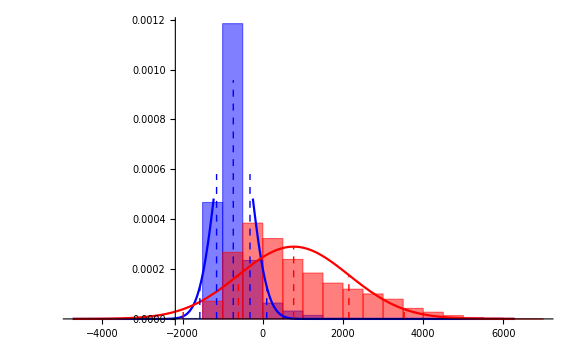

```mathematica
DistributeShow[fr_,fo_]:=Module[{σ1=StandardDeviation[fo],σ2=StandardDeviation[fr],μ1=Mean[fo],μ2=Mean[fr]},
Show[{Histogram[{friend,foreign},Automatic,"PDF",ChartStyle->{Blue,Red}],
Plot[{PDF[NormalDistribution[μ2,σ2],x],PDF[NormalDistribution[μ1,σ1],x]},{x,μ1-4Max[σ1,σ2],μ1+4Max[σ1,σ2]},PlotStyle->{Blue,Red}],
Graphics[{Dashed,Blue,
Table[Line[{{n *σ2+μ2,0},{n *σ2+μ2,PDF[NormalDistribution[μ2,σ2],n *σ2+μ2]}}],{n,-3,3}],
Red,
Table[Line[{{k* σ1+μ1,0},{k*σ1+μ1,PDF[NormalDistribution[μ1,σ1],k *σ1+μ1]}}],{k,-3,3}]}]

},
PlotRange->All,ImageSize->Large]];
DistributeShow[friend,foreign]
```

Проделаем тоже самое  и  получим  график  для скан - столбца, скан - строки и пикселя :

1) Скан-строка:

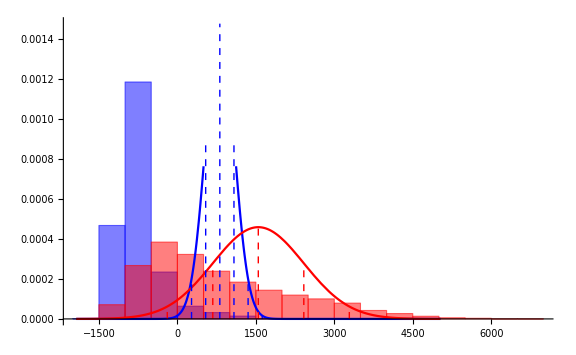

```mathematica
friend1=rowData⟦Dcoord⟦digit⟧⟧;
foreign1=rowData⟦Complement[Range[10000],Dcoord⟦digit⟧]⟧;
DistributeShow[friend1,foreign1]
```

2) Скан-столбец

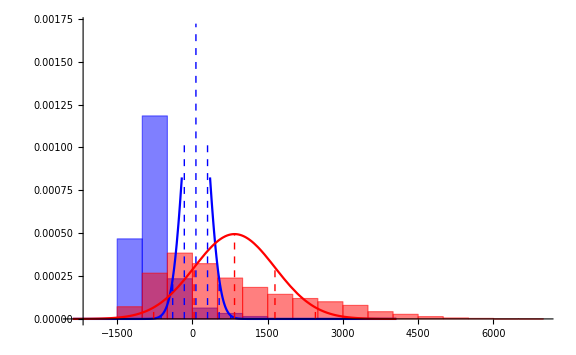

```mathematica
friend2=colData⟦Dcoord⟦digit⟧⟧;
foreign2=colData⟦Complement[Range[10000],Dcoord⟦digit⟧]⟧;
DistributeShow[friend2,foreign2]
```

3) Пиксель

```mathematica
friend3=data⟦Dcoord⟦digit⟧⟧;
foreign3=data⟦Complement[Range[10000],Dcoord⟦digit⟧]⟧;
DistributeShow[friend3,foreign3]
```

-Graphics-

Проанализировав все графики,  наилучшим параметром из  рассмотренных  по-прежнему  остаеться скан-крест. Т.к он наиболее  точно и  наглядно  распределяет объекты  на  “свои” и “чужие”.

То,  что  делали  на паре(выделение главной компоненты)

```mathematica
Module[{F=OpenRead["t10k-images.idx3-ubyte",BinaryFormat->True],FDummy,Counter,Rows,Cols},
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
TestImage=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}];
Close[F]];
Module[{F=OpenRead["t10k-labels.idx1-ubyte",BinaryFormat->True],FDummy,Counter},
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
TestLabel=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F]];
```

```mathematica
{Rows,Cols}=Dimensions[X=X0];
PC={};
```

```mathematica
Do[AppendTo[PC,Module[
{sNew=0,sOld=∞,P,T=X⟦All,Part[Position[#,Max@#]&@Table[#.#&@X⟦All,c⟧,{c,Cols}],1,1]⟧},
Monitor[While[sNew<10.^6 Abs[sNew-sOld],
P=Normalize[T.X];
T=X.P;
{sOld,sNew}={sNew,Norm@T}],Row@{
MatrixPlot[Partition[P,28],PlotRange->All,ImageSize->300,ColorFunction->"GreenPinkTones"],
ListPlot[T,PlotLabel->StringForm["σ=``, Δσ=``",sNew,Abs[sNew-sOld]],PlotRange->All,ImageSize->300]}
];{sNew,T,P}]];
CellPrint@Row@{
MatrixPlot[Partition[PC⟦-1,3⟧,28],PlotRange->All,ImageSize->300,ColorFunction->"GreenPinkTones"],
ListPlot[PC⟦-1,2⟧,PlotLabel->StringForm["σ_(``)=``",n,PC⟦-1,1⟧],PlotRange->All,ImageSize->300]};
Timing@Monitor[Do[X⟦r⟧-=PC⟦-1,2,r⟧PC⟦-1,3⟧,{r,Rows}],ProgressIndicator[r,{1,Rows}]->r],{n,16}];
```

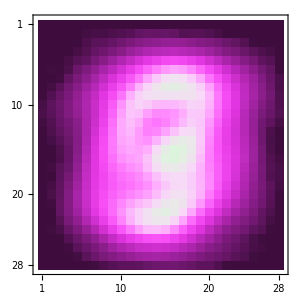
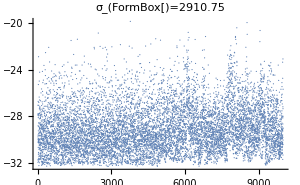

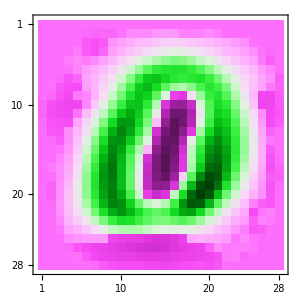
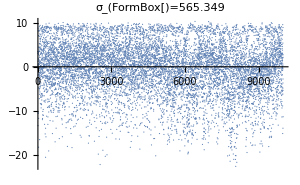

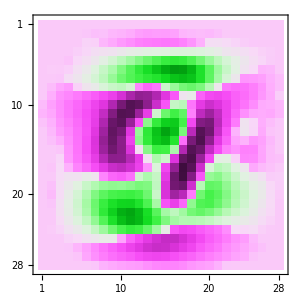
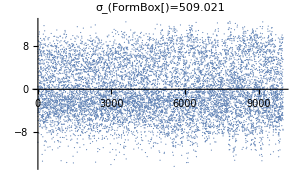

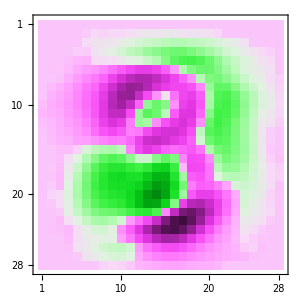
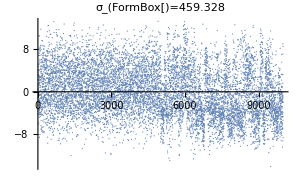

```mathematica
Dimensions[PC]
```

{16,3}

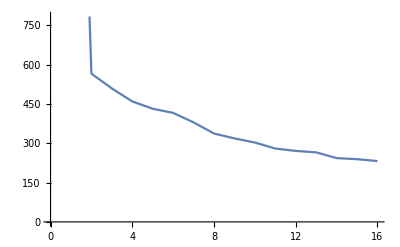

```mathematica
ListLinePlot[PC[[All,1]]]
```